## Chapter 3 Functions and Their Graphs

### Section 3.2

In each part only the value of a constant changes, from 1 to 1.4 to π/2 (which is approximately 1.57), to 2. As the value of the constant increases, note that the “little dips” in the graph get bigger, and then (once the value of the constant surpasses π/2) the “big dips” get smaller.

sin(1+cos(x))

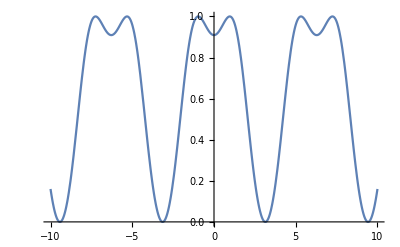

```mathematica
Plot[Sin[1+Cos[x]],{x,-10,10}]
```

sin(1.4+cos(x))

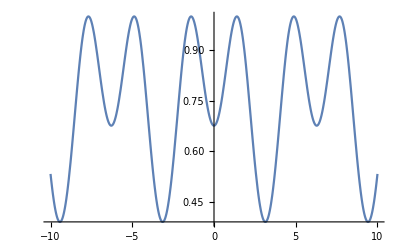

```mathematica
Plot[Sin[1.4+Cos[x]],{x,-10,10}]
```

sin(π/2+cos(x))

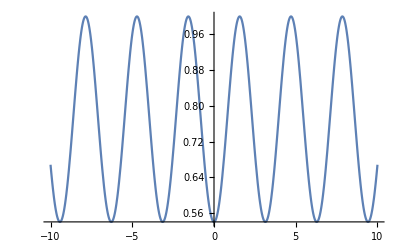

```mathematica
Plot[Sin[π/2+Cos[x]],{x,-10,10}]
```

sin(2+cos(x))

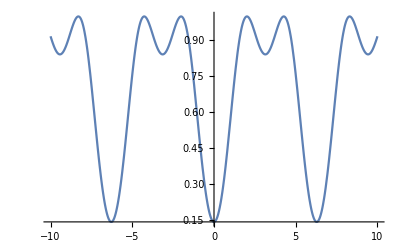

```mathematica
Plot[Sin[2+Cos[x]],{x,-10,10}]
```

Here we have δ=1:

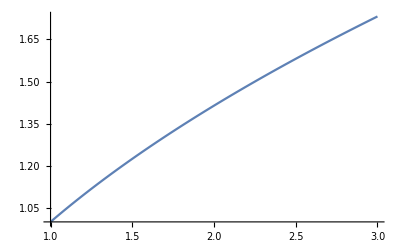

```mathematica
With[{δ=10^0},Plot[√x,{x,2-δ,2+δ}]]
```

We show only the last value: δ=10^-5.

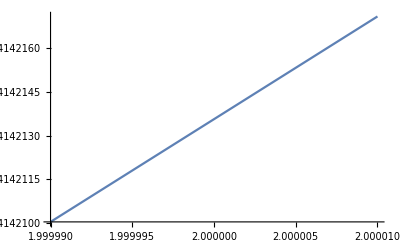

```mathematica
With[{δ=10^-5},Plot[√x,{x,2-δ,2+δ}]]
```

It would appear from the plot that √2≈1.41421. This is correct to six significant digits:

```mathematica
N[√2]
```

1.41421

The two numbers 2-10^-20 and 2+10^-20 that are the endpoints of our domain round to the same machine-precision number. The error message is similar to the one you would see if you asked for a plot with domain specification {x, 2, 2}.

```mathematica
With[{δ=10^-20},Plot[√x,{x,2-δ,2+δ}]]
```

Plot::plld: Endpoints for Charting`Private`pvar$66801 in {Charting`Private`pvar$66801,199999999999999999999/100000000000000000000,200000000000000000001/100000000000000000000} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[√x,{x,2-1/100000000000000000000,2+1/100000000000000000000}]

Just plotting the expression x^(4/5) will leave the left half of the plot empty, for Mathematica regards this as a complex-valued function. Use Surd[x^4,5] or use EscsurdEsc to format (x^4)^(1/5)  to plot this function when the domain includes negative numbers. Note that f(32)=32^(4/5)=(32^(1/5))^4=2^4=16, which is what the plot shows.

```mathematica
f[x_]:=(x^4)^(1/5)
```

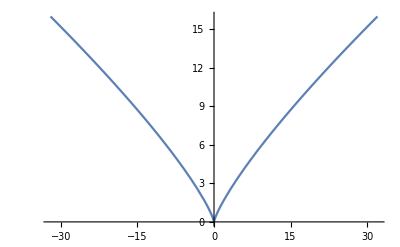

```mathematica
Plot[f[x],{x,-32,32}]
```

```mathematica
f[32]
```

16

### Section 3.3

This is one way to do it. Note that the options may be given in any order.

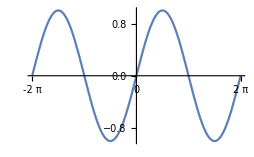

```mathematica
Plot[Sin[x],{x,-2π,2π},GridLines->{Range[-2π,2π,π/4],Range[-1,1,.2]},Ticks->{Range[-2π,2π,π],Automatic},GridLinesStyle->Lighter[Gray]]
```

This is one way to do it. Note that the options may be given in any order.

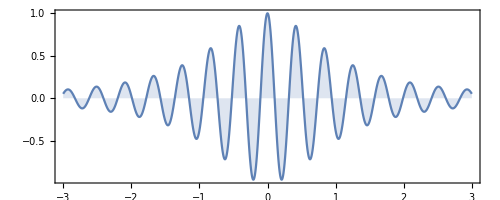

```mathematica
Plot[Cos[15 x]/(1+x^2),{x,-3,3},Filling->Axis,PlotRange->All,Axes->{True,False},Frame->{True,True,False,False},FrameStyle->GrayLevel[.5],AspectRatio->Automatic]
```

This color setting was obtained from the Insert ⊳ Color… dialog.

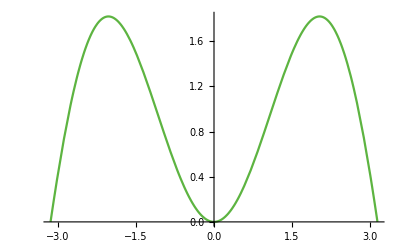

```mathematica
Plot[x*Sin[x],{x,-π,π},PlotStyle->RGBColor[0.363012, 0.704662, 0.253071]]
```

There is a tiny gap in the graph above x=1. If ExclusionsStyle had been set to Red, there would be a very small red segment joining the two pieces of the graph. It is likely that this red bridge would be invisible unless the graphic were enlarged significantly.

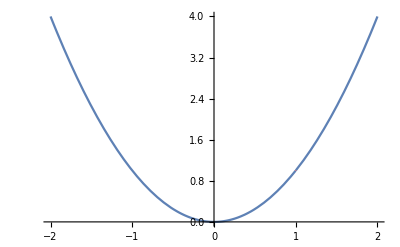

```mathematica
Plot[x^2,{x,-2,2},Exclusions->{x==1},ExclusionsStyle->Red]
```

We take advantage of the Listable attribute of the Sqrt function, to create a list of the form {√0,√10,√20,…}.

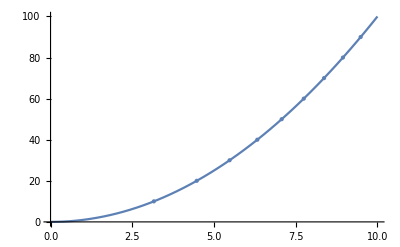

```mathematica
Plot[x^2,{x,0,10},Mesh->9,MeshFunctions->{#2&},GridLines->{√Range[0,100,10],Range[0,100,10]}]
```

Note that the default setting for MeshFunctions is {#1&}, so it is not necessary to change this when equally spaced x values are needed. We now take advantage of the Listable attribute of the Power function to make the y-list.

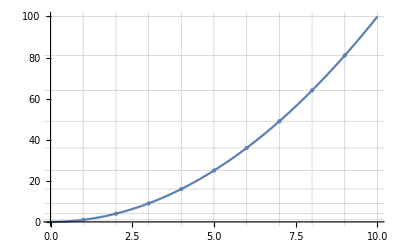

```mathematica
Plot[x^2,{x,0,10},Mesh->9,GridLines->{Range[0,10],Range[0,10]^2}]
```

Set the mesh function to be the difference between the two functions being plotted, and set the value of this difference to be 0. The Mesh setting is {{0}} since we are specifying a (rather short) list of specific values to be assumed by the (first and only) mesh function in our list of MeshFunctions.

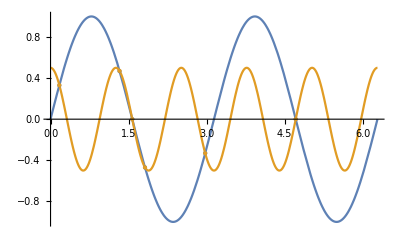

```mathematica
Plot[{Sin[2x],1/2 Cos[5x]},{x,0,2π},Mesh->{{0}},MeshFunctions->{Sin[2#1]-1/2 Cos[5#1]&}]
```

### Section 3.4

Create a single variable (we call ours pt), and give it a specification that ranges from lower-left to upper-right, like this:

```mathematica
Manipulate[pt,{pt,{-1,-1},{1,1}}]
```

Here it is:

```mathematica
Manipulate[
Plot[Sin[x]^2,{x,0,2π},AspectRatio->aspectratio,ImageSize->{Automatic,128}],
{aspectratio,.2,10}]
```

The RGB color space is explored here:

```mathematica
Manipulate[
Plot[Sin[x]^2,{x,0,2π},Frame->True,Background->RGBColor[red,green,blue]],{{red,.8},0,1},{{green,1},0,1},{blue,0,1}]
```

The HSBcolor space is explored here:

```mathematica
Manipulate[
Plot[Sin[x]^2,{x,0,2π},Frame->True,Background->Hue[hue,saturation,brightness]],{hue,0,1},{{saturation,1},0,1},{{brightness,1},0,1}]
```

The two strings become one:

```mathematica
"This is a string"~~" and so is this."//FullForm
```

"This is a string and so is this."

A single string is created, where two portions of the string are tied to the Manipulate variable x. The string is displayed in the "Subsubsection" style of the current notebook.

```mathematica
Manipulate[Style["The square root of "~~ToString[x]~~" is "~~ToString[N[√x]]~~".","Subsubsection"],
{{x,2},1,10}]
```

An Epilog was also added to display the point on the graph whose coordinates are given. This option to the Plot command is discussed in Section 3.10. Note also that Chop was wrapped around the value of the sine function. While not necessary, this has the effect of rounding tiny numbers to zero so that the display is correct when the slider is all the way to one side or the other.

```mathematica
Manipulate[Plot[Sin[t],{t,-π,π},Epilog->Point[{x,Sin[x]}],PlotLabel->Style["sin("~~ToString[x] ~~") = " ~~ToString[Chop@N[Sin[x]]] ~~".","Text"]],
{x,-π,π}]
```

We specify a radius of 0.05 for the Circle. Its center is controlled by the Locator.

```mathematica
Manipulate[Graphics[{Directive[Thick,Blue],Circle[pt,.05]},Axes->True,PlotRange->1],
{{pt,{0,0}},Locator,Appearance->None}]
```

We replace Plot by Grid to obtain the following:

```mathematica
Manipulate[
ToExpression[SymbolName[option]~~"::usage"],
{option,Map[First,Options[Grid]]}]
```

The inputs and outputs below illustrate the ideas.

```mathematica
Options[Grid]
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic}

```mathematica
Map[First,Options[Grid]]
```

{Alignment,AllowedDimensions,AllowScriptLevelChange,AutoDelete,Background,BaselinePosition,BaseStyle,DefaultBaseStyle,DefaultElement,DeleteWithContents,Dividers,Editable,Frame,FrameStyle,ItemSize,ItemStyle,Selectable,Spacings}

```mathematica
ToExpression["ItemSize::usage"]
```

ItemSize is an option for Grid, Column, and related constructs that specifies the sizes to allow for items.

```mathematica
ToExpression[SymbolName[ItemSize]~~"::usage"]
```

ItemSize is an option for Grid, Column, and related constructs that specifies the sizes to allow for items.

Note the use of \t below. This is how the ⇥ character is encoded in a string. The three tabs move the answer text near the center of the panel.

```mathematica
TabView[{"Riddle"->Style["I'm a wave that does not move, and to you I want to prove, that if you knock I'm hard as rock and if you kick me I'll stick to your sock.",Italic, "Text"],
"Answer"->Style["\t\t Ice!","Section"]}]
```

12

Here are two simple examples:

```mathematica
Manipulate[{x,y},"X1"->{x,0,1},"Y1"->{y,0,1}]
```

```mathematica
Manipulate[pt,"XY1"->{pt,{-1,-1},{1,1}}]
```

### Section 3.5

The list produced by the first input is broken into a list of ten sublists, suitable as input to Grid.

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Partition[Range[100],10]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100}}

The output of Partition is suitable as input to Grid.

```mathematica
Text@Grid@Partition[Range[100],20]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

While it is easiest to use Partition as above, the input below produces the same output.

```mathematica
Text@Grid@Table[Range[n,n+19],{n,1,81,20}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

This also works, but we reiterate that Partition is the easiest means to accomplish this result.

```mathematica
Text@Grid@Table[Table[n+k,{k,0,19}],{n,1,81,20}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

We evaluate all four inputs in a single list:

```mathematica
{Style[4,Red],Style[4,72],Style[4,"Title"],Style[4,FontFamily->"Helvetica",FontWeight->"Bold"]}
```

{4,4,4,4}

Each column in the grid gives successively higher powers of a number. So we have:

```mathematica
Style[Grid@Table[{n,n^2,n^3,n^4},{n,5}],FontFamily->"Comic Sans MS",Blue]
```

1 | 1 | 1 | 1
2 | 4 | 8 | 16
3 | 9 | 27 | 81
4 | 16 | 64 | 256
5 | 25 | 125 | 625

Just create a Grid as below, select the cell bracket, then visit the Format menu.

```mathematica
Grid@Table[{n,n^2,n^3,n^4},{n,5}]
```

1 | 1 | 1 | 1
2 | 4 | 8 | 16
3 | 9 | 27 | 81
4 | 16 | 64 | 256
5 | 25 | 125 | 625

If you enter ?*Q you will see that PrimeQ is one of dozens of query commands (we won’t show that output here, as it is rather large). There are even more query commands that do not end in the letter Q, (e.g., Positive, NonNegative, etc.)

```mathematica
?P*Q
```

The prime numbers are shown in red.

```mathematica
Table[If[PrimeQ[n],Style[n,Red],n],{n,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

We use Partition to break the above list into ten rows of ten. Note how the Style settings persist even when embedded in other commands. Note also that this one-line input generates something that would not be easily produced, for instance, by a spreadsheet.

```mathematica
Text@Grid@Partition[Table[If[PrimeQ[n],Style[n,Red],n],{n,100}],
10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

We proceed using the same ideas as above, but using the SquareFreeQ command.

```mathematica
Text@Grid@Partition[Table[If[SquareFreeQ[n],Style[n,Blue,Underlined],n],{n,100}],
10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

This time the PrimePowerQ command is called for. To save space we display only the first ten rows.

```mathematica
Text@Grid@Partition[Table[If[PrimePowerQ[n],Style[n,Orange,Italic],n],{n,200}],
20]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100
101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120
121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140
141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160
161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180
181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200

Each summand is of the form n^3, and n ranges from 1 to 20.

```mathematica
Sum[n^3,{n,20}]
```

44100

Now replace the power 3 above by x.

```mathematica
Clear[f,x];
f[x_]:=Sum[n^x,{n,20}];
Grid[Table[{x,f[x]},{x,10}],Dividers->Gray]
```

1 | 210
2 | 2870
3 | 44100
4 | 722666
5 | 12333300
6 | 216455810
7 | 3877286700
8 | 70540730666
9 | 1299155279940
10 | 24163571680850

Note that the option PlotRange → All is needed to see the far right portion:

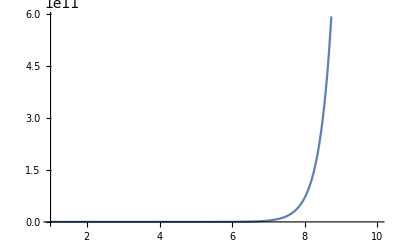

```mathematica
Plot[f[x],{x,1,10}]
```

```mathematica
Clear[f]
```

See  the exercise 7 below.

First create a table of invisible items:

```mathematica
emptyTable=Partition[Table[" ",{100}],10];
```

Each output is shown:

```mathematica
Grid[emptyTable,Dividers->Gray]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Dotted]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Thick]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Directive[Thin,Orange]]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

The setting {Black, {Gray}, Black} determines the vertical dividers. The first is Black, all of the middle ones are Gray (the extra set of brackets means “repeat this directive”), and the last is Black again. There are no horizontal dividers.

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},None}
]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

Here are two means of producing the output:

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},{Black,Black,{None},Black}}
]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->{{True,{Gray},True},{True,True,{False},True}}
]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

There are no background directives applied to the columns. The first row is light gray, while the next rows repeat a light blue / light yellow pattern (the extra curly brackets around these two settings mean that they are to be repeated).

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},{Black,Black,{None},Black}},
Background->{None,{Lighter[Gray,.7],{Lighter[Blue,.9],Lighter[Yellow,.9]}}}
]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

The first input below is a first attempt (prior to formatting). The second column is fine (at least it will be once it is aligned), but the first column is not. We need to prevent Mathematica from evaluating 10^n. We do this by replacing n with ToString[n]. The resulting string, "3" for example, looks like a number (the double quotes do not show in default StandardForm output), but does not behave like one. The final version is given in the second input below. The gridData is modified to fix the entries in the first column. We then use appropriate Dividers, Background, Alignment, and ItemStyle options in Grid to construct the table.

```mathematica
Clear[gridData];
gridData=Table[{10^n,10.^n},{n,-5,5}];
Grid@gridData
```

1/100000 | 0.00001
1/10000 | 0.0001
1/1000 | 0.001
1/100 | 0.01
1/10 | 0.1
1 | 1.
10 | 10.
100 | 100.
1000 | 1000.
10000 | 10000.
100000 | 100000.

```mathematica
With[{
gridData=Table[{10^ToString[n],10.^n},{n,-5,5}]},
Text@Grid[gridData,
Dividers->{Black,{Black,{Gray},Black}},
Background->{{Blue,None},{{Lighter[Blue,.9],Lighter[Yellow,.9]}}},
Alignment->{{Left,"."},Baseline},
ItemStyle->{{{{FontFamily->"Helvetica",FontColor->White}},Black},None}
]]
```

10^-5 | 0.00001
10^-4 | 0.0001
10^-3 | 0.001
10^-2 | 0.01
10^-1 | 0.1
10^0 | 1.
10^1 | 10.
10^2 | 100.
10^3 | 1000.
10^4 | 10000.
10^5 | 100000.

```mathematica
Clear[emptyTable,gridData]
```

Within the Manipulate we place a Grid of the form

Grid[{{top left plot , top right text},{bottom left plot , bottom right text}}].

The input below contains comments between (* and *) to make it easier to understand where the brackets and commas are within this overall Grid structure, since two of the four items are somewhat complex. Note also that you can triple-click an opening bracket or command name to select the scope that it determines.

```mathematica
Manipulate[
Grid[{{
(* top left *)
Plot[Sin[x],{x,-π,π},
AspectRatio->Automatic,
Ticks->{{-π,-π/2,π/2,π},{-1,1}},
Epilog->{Red,PointSize[.02],Point[{x0,Sin[x0]}]}],
(* top right *)
Style["Full View","Subsubsection"]
},{
(* bottom left *)
Plot[Sin[x],{x,x0-δ,x0+δ},
Axes->False,
GridLines->Automatic,
AspectRatio->Automatic,
Frame->True,
Epilog->{Red,PointSize[.02],Point[{x0,Sin[x0]}]}],
(* bottom right *)
Style["Zoom View","Subsubsection"]
}}],
(* Manipulate controls *)
{{x0,0.,"Center"},-2,2},{{δ,1.,"Zoom Level"},10^-10,2}]
```

We follow the example in the text, using CurrencyConvert.

```mathematica
Manipulate[
Grid[{{Quantity[c,"Euros"]," = ",CurrencyConvert[Quantity[c,"Euros"],Quantity["USDollars"]]}},ItemSize->{4,3},Alignment->{Center,Center}],
{{c,10},0,100,.01}]
```

### Section 3.6

The last condition effectively means “everywhere else” so True will always work.

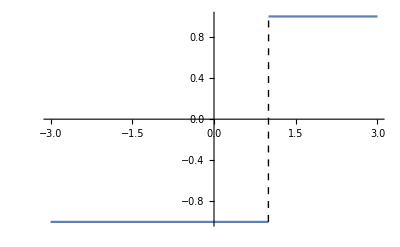

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, True}}],{x,-3,3},ExclusionsStyle->Dashed]
```

The function is 0 except when 0<x<3, so we make our plot on this interval. The function is comprised of three parabolas on this domain, but they fit together not only continuously, but smoothly. In loose terms, there are no sharp corners in the plot. In more technical terms (for those who have had some calculus), we say that f is differentiable.

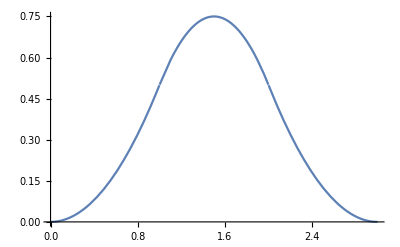

```mathematica
Plot[Piecewise[{{0, x<0}, {x^2/2, 0≤x<1}, {-x^2+3 x-3/2, 1≤x<2}, {1/2 (3-x)^2, 2≤x<3}, {0, 3≤x}}],{x,0,3}]
```

Here it is convenient to use the standard syntax, with Table employed to generate the Piecewise argument. Each item in the table is of the form {value,domain}. The Exclusions option is needed in this case to remove the vertical lines between steps.

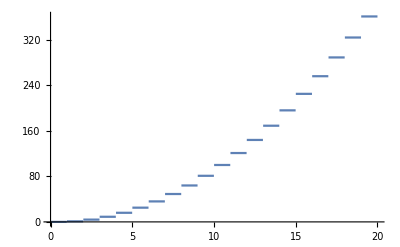

```mathematica
Plot[Piecewise[Table[{n^2,n≤x<n+1},{n,0,19}]],{x,0,20},Exclusions->Range[19]]
```

### Section 3.7

Be sure to put a space between the x and the y inside the sine function (or just type *).

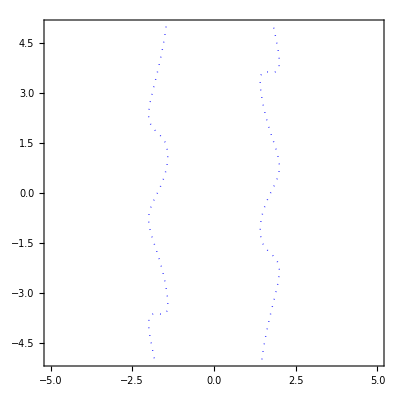

```mathematica
ContourPlot[x^2-Sin[x*y]==3,{x,-5,5},{y,-5,5},ContourStyle->Directive[Thick,Blue,Dotted]]
```

Notice that when you mouseover any curve in the output, the value corresponding to that curve is displayed as a Tooltip. In this case the curves are hyperbolas with a vertical axis when the values are negative, hyperbolas with a horizontal axis when the values are positive, and the lines y=±x when the value is 0.

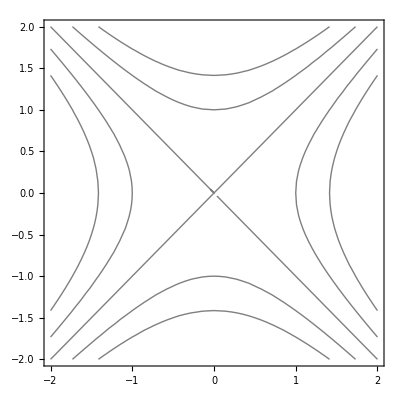

```mathematica
ContourPlot[x^2-y^2,{x,-2,2},{y,-2,2},Contours->{-2,-1,0,1,2},ContourShading->False]
```

The following input is all that is needed:

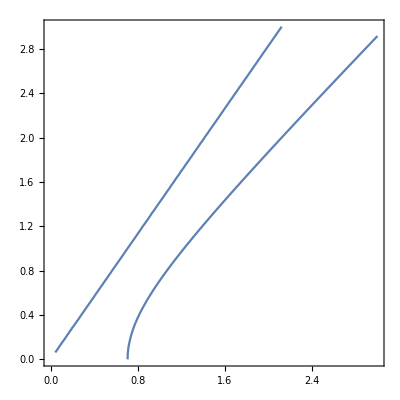

```mathematica
ContourPlot[Piecewise[{{x^2-y^2,y<x},{1-x^2/y^2,y>x}}]==1/2,{x,0,3},{y,0,3}]
```

### Section 3.8

One: Extend the domain. The oscillatory behavior of the second function is now revealed (it has a zero at every integer multiple of π). Note its color, and you are done (see the first input below). Two: Set the PlotTheme to “Detailed”. This will add a legend to the plot (see the second input below). Three: Specify color (or other distinguishing) Graphics directives via the PlotStyle option. The first function picks up the first directive, and the second picks up the second (see the third input below). Four: Think like a mathematician! For all positive numbers x, it is always the case that sin(x)<x. It’s true—you can prove it. After you do, multiply both sides by x to see that x sin(x)<x^2.

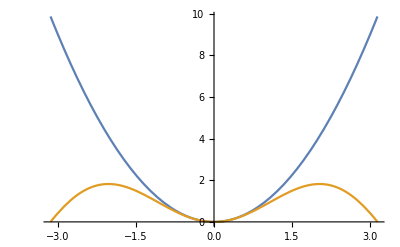

```mathematica
Plot[{x^2,x Sin[x]},{x,-π,π}]
```

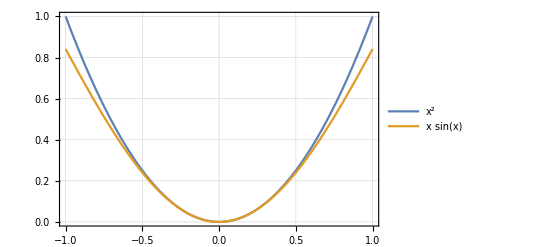

```mathematica
Plot[{x^2,x Sin[x]},{x,-1,1},PlotTheme->"Detailed"]
```

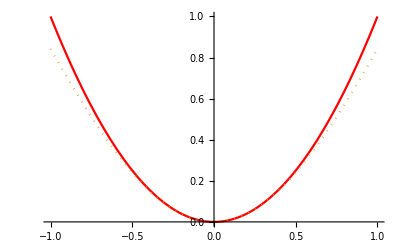

```mathematica
Plot[{x^2,x Sin[x]},{x,-1,1},PlotStyle->{Red, Dotted}]
```

The two functions appear to be identical (the blue function shows between the dashes of the red one).

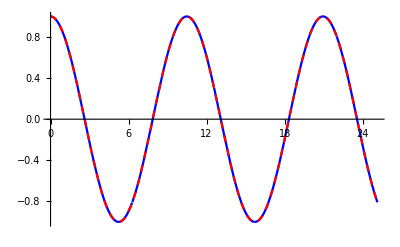

```mathematica
Plot[{(Sin[.4 t]+Sin[1.6t])/(2 Sin[t]),Cos[.6t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

These are also identical.

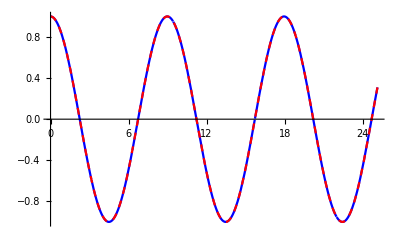

```mathematica
Plot[{(Sin[.3 t]+Sin[1.7t])/(2 Sin[t]),Cos[.7t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

These are also identical.

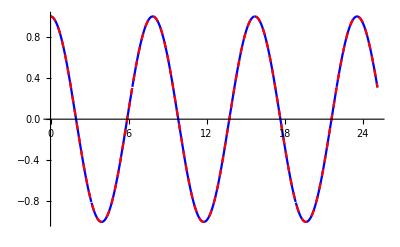

```mathematica
Plot[{(Sin[.2 t]+Sin[1.8t])/(2 Sin[t]),Cos[.8t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

It appears that (sin(k t)+sin((2-k) t))/(2sin(t))=cos((1-k)t) for any real numbers k and t, where t is not an integer multiple of π.

We will refer to the first two functions being plotted as the component functions. The component functions are not defined when t is an integer multiple of π; they typically will have vertical asymptotes at these values of t, but not always (see t=5π with the initial value k=.4 below). For any value of t which is not an integer multiple of π, the sum of the values of the component functions is cos((1-k)t), which is bounded (it never assumes values greater than 1 or less than -1). So at any point t where one component function assumes a large positive value y (near an asymptote, for instance), the other component function must assume a value within two units of -y. Another observation: at any point t where the graph of cos((1-k)t) crosses the graph of one of the component functions, the other component function is zero (i.e., is crossing the x axis). And the two component functions always intersect at a height which is exactly half way between the x axis and the graph of cos((1-k)t).

```mathematica
Manipulate[
Plot[{Sin[k t]/(2 Sin[t]),Sin[(2-k)t]/(2 Sin[t]),Cos[(1-k)t]},{t,0,8π},PlotRange->2,PlotStyle->{Darker[Gray],Darker[Pink],Directive[Thick,Black]},GridLines->{Range[0,8π,π],{}},Ticks->None,Filling->{1->Axis,2->Axis}],{{k,.4},0,2}]
```

We first set the options to Plot, so that we don’t have to re-type them each time. We define a command myStyle to display text in the Subsubsection style. This is not necessary, but it saves us from a bit of extra typing. We use p=1 and choose generic values for n for each function. It looks like a lot of typing, but once one row is done, it can be copied and pasted, then modified slightly.

```mathematica
plotOpts=Options[Plot];
SetOptions[Plot,Ticks->None,AxesOrigin->{0,0},ImageSize->70];
myStyle[txt_]:=Style[txt,"Subsubsection",7];
Grid[{
{myStyle["Plot of p*x^n looks like:"],myStyle["When:"],myStyle["Plot of -p*x^n looks like:"],myStyle["When:"]},

{Plot[x^2,{x,0,4}],myStyle["n>1"],Plot[-x^2,{x,0,4}],myStyle["n>1"]},

{Plot[x,{x,0,4}],myStyle["n=1"],Plot[-x,{x,0,4}],myStyle["n=1"]},

{Plot[x^(.5),{x,0,4}],myStyle["0<n<1"],Plot[-x^(.5),{x,0,4}],myStyle["0<n<1"]},

{Plot[x^-1,{x,0,4}],myStyle["n<0"],Plot[-x^-1,{x,0,4}],myStyle["n<0"]}
},Dividers->{{Gray,False,Gray,False,Gray},Gray},Spacings->3]
```

Plot of p*x^n looks like: | When: | Plot of -p*x^n looks like: | When:
-Graphics- | n>1 | -Graphics- | n>1
-Graphics- | n=1 | -Graphics- | n=1
-Graphics- | 0<n<1 | -Graphics- | 0<n<1
-Graphics- | n<0 | -Graphics- | n<0

```mathematica
SetOptions[Plot,plotOpts];
Clear[plotOpts,myStyle]
```

### Section 3.9

The radius {4,2} setting creates an ellipse with horizontal “radius” 4, and vertical “radius” 2. Traditionally we refer to these values as the semimajor and semiminor axis lengths.

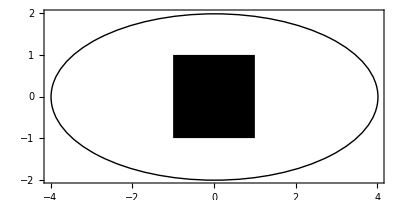

```mathematica
Graphics[{
Circle[{0,0},{4,2}],
Rectangle[{-1,-1},{1,1}]
},Frame->True]
```

Yes, it is indeed a red disk.

```mathematica
Graphics[{Red,Disk[]}]
```

-Graphics-

This simply changes the color directive.

```mathematica
Graphics[{Lighter[Blend[{Blue,Red},.3],.4],Disk[]}]
```

-Graphics-

Here it is:

```mathematica
Manipulate[Graphics[{Lighter[Blend[{Blue,Red},r],s],Disk[]}],{{r,.5,"proportion red"},0,1},{{s,.2,"lightness"},0,1}]
```

We apply the Opacity[x] directive to the second disk, where x is a Manipulate variable. Note that since it is listed second, the disk with variable opacity is placed on top of the first disk.

```mathematica
Manipulate[
Graphics[{
{Blue,Disk[]},
{Opacity[x],Disk[{1,0},1]}
}],
{{x,.5,"opacity"},0,1}]
```

Repeat the previous part, but make the second disk (the one with varying opacity) orange.

```mathematica
Manipulate[
Graphics[{
{Blue,Disk[]},
{Directive[Orange,Opacity[x]],Disk[{1,0},1]}
}],
{{x,.5,"opacity"},0,1}]
```

The radius {1, r} creates an ellipse with horizontal axis of “radius” 1, and vertical axis of “radius” r. As r varies, this looks a bit like a mouth.

```mathematica
Manipulate[Graphics[{Thickness[.02],Circle[{0,0},{1,r},{π,2π}]}],
{{r,.8},0.01,1}]
```

See below.

Here’s one version of the final product. Note that adding a color field to change the color from yellow to anything else can easily be done.

```mathematica
Manipulate[Graphics[{
{Yellow,Disk[{0,0},1.3]},
Disk[{-.3,.5},{.1,.2}],
Disk[{.3,.5},{.1,.2}],
{Thickness[.02],Line[{{-.5,1.5-h},{-.1,h}}]},
{Thickness[.02],Line[{{.5,1.5-h},{.1,h}}]},
{Thickness[.02],Circle[{0,0},{1,r},{π,2π}]}
}],{{r,.5,"mouth"},.01,1},{{h,.8,"eyebrows"},.5,1}]
```

The Circle command can be used to create an ellipse. Rather than specifying a single positive radius, give as the second argument to Circle a list with two items: the lengths of the x and y radii. That is, the larger of these numbers is the length of the semimajor axis, while the smaller is the length of the semiminor axis.

The horizontal radius is 2 and the vertical radius is 3:

```mathematica
Graphics[Circle[{0,0},{2,3}],Axes->True]
```

-Graphics-

We define the kth ellipse, and then make a Table of them.

```mathematica
ellipse[k_]:=Circle[{0,0},{√((k(20-k+1))/(20+2)),√(((20-k+1) (20-k+2))/((20+1) (20+2)))}]
```

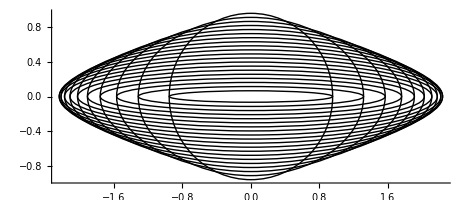

```mathematica
Graphics[Table[ellipse[k],{k,20}],Axes->True]
```

Yes it is; for k=1 both semiaxes have length √(10/11).

A table shows that for both k=10 and k=11 the semimajor axis assumes its greatest value of approximately 2.236. This is consistent with the graphic. Note the syntax for highlighting the background for two rows in the table.

```mathematica
Text@Grid[Table[{k,√((k(20-k+1))/(20+2))//N},{k,20}],Dividers->All,Alignment->".",Spacings->3,Background->{None,{10->Lighter[Gray],11->Lighter[Gray]}}]
```

1 | 0.953463
2 | 1.31426
3 | 1.5667
4 | 1.7581
5 | 1.90693
6 | 2.0226
7 | 2.11058
8 | 2.17423
9 | 2.21565
10 | 2.23607
11 | 2.23607
12 | 2.21565
13 | 2.17423
14 | 2.11058
15 | 2.0226
16 | 1.90693
17 | 1.7581
18 | 1.5667
19 | 1.31426
20 | 0.953463

```mathematica
Clear[ellipse]
```

### Section 3.10

We enter the data, find the best-fitting function, and plot it, using three inputs.

```mathematica
data={{1, 1.2}, {2, 2.3}, {3, 3.6}, {4, 4.9}, {5, 5.9}};
```

```mathematica
Clear[x];
Fit[data,{1,x},x]
```

-0.02+1.2 x

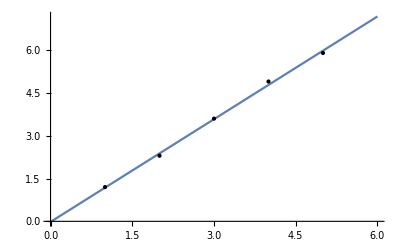

```mathematica
Plot[%,{x,0,6},Epilog->Point[data]]
```

Use FindFit after entering the data as above. We find that n is very close to 1, so the resulting function is very nearly a straight line.

```mathematica
Clear[p,n,x];
FindFit[data,p*x^n,{p,n},x]
```

{p→1.18974,n→1.00295}

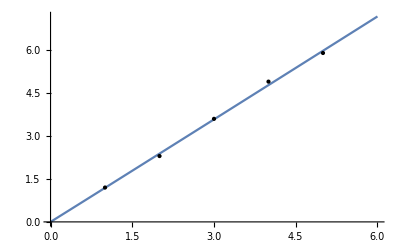

```mathematica
Plot[1.18974*x^1.00295,{x,0,6},Epilog->Point[data]]
```

We use Table to make a Grid where the first column gives the x-coordinates of the data, and for each such coordinate, the remaining rows show the y-coordinate of the data, the value of the fit function, and the residual. This is done twice, first for the linear function, then again for the power function.

```mathematica
Text@Grid[Prepend[Table[{x,data⟦x,2⟧,-0.02+1.2 x,data⟦x,2⟧-(-0.02+1.2 x)},{x,data⟦All,1⟧}],{"x","y","Predicted","Residual"}],Alignment->Right]
```

x | y | Predicted | Residual
1 | 1.2 | 1.18 | 0.02
2 | 2.3 | 2.38 | -0.08
3 | 3.6 | 3.58 | 0.02
4 | 4.9 | 4.78 | 0.12
5 | 5.9 | 5.98 | -0.08

```mathematica
Text@Grid[Prepend[Table[{x,data⟦x,2⟧,1.18974*x^1.00295,data⟦x,2⟧-(1.18974*x^1.00295)},{x,data⟦All,1⟧}],{"x","y","Predicted","Residual"}],Alignment->Right]
```

x | y | Predicted | Residual
1 | 1.2 | 1.18974 | 0.01026
2 | 2.3 | 2.38435 | -0.0843505
3 | 3.6 | 3.58081 | 0.0191937
4 | 4.9 | 4.77846 | 0.121538
5 | 5.9 | 5.97701 | -0.0770106

The command works by generating a ListPlot of the raw data together with the values of the function (calculated using Table). The option setting Filling → {1 → {2}} draws vertical fill-lines between the two. It then makes a Plot of the function, and uses Show to display them together. The FillingStyle option specifies that green line segments are used for positive residuals, and red segments for negative residuals.

```mathematica
residualPlot[data_,function_,{x_,xmin_,xmax_},opts___Rule]:=Show[
ListPlot[{data,Table[{x,function},{x,data⟦All,1⟧}]},Filling->{1->{2}},FillingStyle->{Red,Green},PlotMarkers->{"⋆",""},opts],
Plot[function,{x,xmin,xmax}]
]
```

```mathematica
data={{1, 1.2}, {2, 2.3}, {3, 3.6}, {4, 4.9}, {5, 5.9}};
```

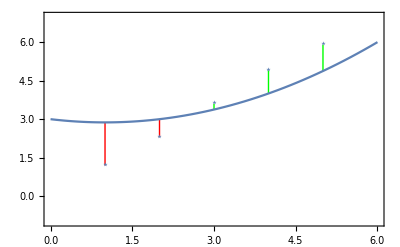

```mathematica
residualPlot[data,3-.25x+.125 x^2,{x,0,6},Axes->False,Frame->True,PlotRange->{{0,6},{-1,7}}]
```

```mathematica
Clear[data,residualPlot]
```

### Section 3.11

Outputs are not shown here, as they are rather large. Either of the inputs below will generate a (random) data table of the prescribed dimensions, but feel free to use data of your choosing. Note: The inputs below are not Evaluatable. To use them, just highlight the content and paste into a fresh input cell. Or you could select the cell bracket and in the menus choose Cell > Cell Properties > Evaluatable.

```mathematica
data=Table[RandomInteger[{1,100}],{120},{6}]
```

```mathematica
data=RandomInteger[{1,100},{120,6}]
```

The following will extract the two desired columns:

```mathematica
data⟦All,{2,6}⟧
```

Just use a Span of rows 2 through 120. Alternately, use Rest to throw away the first item, in this case, row 1.

```mathematica
data⟦2;;120,{2,6}⟧
```

```mathematica
data⟦All,{2,6}⟧//Rest
```

Make a copy of the last result, then overwrite the second column:

```mathematica
newData=data⟦2;;120,{2,6}⟧;
newData⟦All,2⟧=Log[data[2;;120,6]];
newData
```

```mathematica
Clear[data,newData]
```

### Section 3.12

To save space we display only the first five rows of the table.

```mathematica
data=Table[{ElementData[n,"Name"],ElementData[n,"AtomicWeight"],ElementData[n,"MolarVolume"]},{n,118}];
```

```mathematica
Text@Grid[Prepend[data⟦1;;5⟧,{"Element","Atomic weight","Molar volume"}],Dividers->Gray]
```

Element | Atomic weight | Molar volume
hydrogen | 1.008 u | 0.011 m^3/mol
helium | 4.002602 u | 0.0224 m^3/mol
lithium | 6.94 u | 0.000013 m^3/mol
beryllium | 9.0121831 u | 4.88×10^-6 m^3/mol
boron | 10.81 u | 4.39×10^-6 m^3/mol

We could also specify the columns using 2;;3.

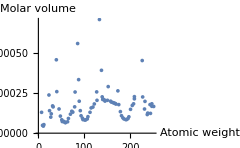

```mathematica
ListPlot[data⟦All,{2,3}⟧,AxesLabel->{"Atomic weight","Molar volume"}]
```

Each coordinate pair {x,y} above has to be replaced by the structure Tooltip[{x,y},name]. The output below will display in print exactly as the previous output, but in a live session the Tooltip will be active.

```mathematica
ListPlot[Table[Tooltip[{ElementData[n,"AtomicWeight"],ElementData[n,"MolarVolume"]},ElementData[n,"Name"]],{n,118}],AxesLabel->{"Atomic weight","Molar volume"}]
```

-Graphics-

```mathematica
Clear[data]
```

To save space we display only the ten most popular names. Note that each “sheet” of an Excel spreadsheet is enclosed in its own set of curly brackets. This means there will be an extra set of curly brackets around our data. The column headings appear in row 3, and the actual data begins in row 4. Below we display rows 3 through 13 (column headings plus 10 rows of data). The iconized data is included below, so no import is needed to work with it, should you wish to do so; just ignore the first input, and enter the second.

```mathematica
SetDirectory[NotebookDirectory[]];
Iconize[Import["Names_2010Census_Top1000.xlsx"],"1000 surnames"]
```

```mathematica
data=;
```

```mathematica
Text@Grid[data⟦1,3;;13⟧,Dividers->Gray]
```

SURNAME | RANK | FREQUENCY (COUNT) | PROPORTION PER 100,000 POPULATION | CUMULATIVE PROPORTION | PERCENT NON-HISPANIC OR LATINO WHITE ALONE | PERCENT NON-HISPANIC OR LATINO BLACK OR AFRICAN AMERICAN ALONE | PERCENT NON-HISPANIC OR LATINO ASIAN AND NATIVE HAWAIIAN AND OTHER PACIFIC ISLANDER ALONE | PERCENT NON-HISPANIC OR LATINO AMERICAN INDIAN AND ALASKA NATIVE ALONE | PERCENT NON-HISPANIC OR LATINO TWO OR MORE RACES | PERCENT HISPANIC OR LATINO ORIGIN
SMITH | 1. | 2.44298×10^6 | 828.19 | 828.19 | 70.9 | 23.11 | 0.5 | 0.89 | 2.19 | 2.4
JOHNSON | 2. | 1.93281×10^6 | 655.24 | 1483.42 | 58.97 | 34.63 | 0.54 | 0.94 | 2.56 | 2.36
WILLIAMS | 3. | 1.62525×10^6 | 550.97 | 2034.39 | 45.75 | 47.68 | 0.46 | 0.82 | 2.81 | 2.49
BROWN | 4. | 1.43703×10^6 | 487.16 | 2521.56 | 57.95 | 35.6 | 0.51 | 0.87 | 2.55 | 2.52
JONES | 5. | 1.42547×10^6 | 483.24 | 3004.8 | 55.19 | 38.48 | 0.44 | 1. | 2.61 | 2.29
GARCIA | 6. | 1.16612×10^6 | 395.32 | 3400.12 | 5.38 | 0.45 | 1.41 | 0.47 | 0.26 | 92.03
MILLER | 7. | 1.16144×10^6 | 393.74 | 3793.86 | 84.11 | 10.76 | 0.54 | 0.66 | 1.77 | 2.17
DAVIS | 8. | 1.11636×10^6 | 378.45 | 4172.31 | 62.2 | 31.6 | 0.49 | 0.82 | 2.45 | 2.44
RODRIGUEZ | 9. | 1.09492×10^6 | 371.19 | 4543.5 | 4.75 | 0.54 | 0.57 | 0.18 | 0.18 | 93.77
MARTINEZ | 10. | 1.06016×10^6 | 359.4 | 4902.9 | 5.28 | 0.49 | 0.6 | 0.51 | 0.22 | 92.91

We make a cumulative frequency plot (column 5 of the data). We find that 23.276% (23276 out of 100000) of respondents have one of the top 200 surnames. We find that 40.968% (40968 out of 100000) of respondents have one of the top 1000 names.

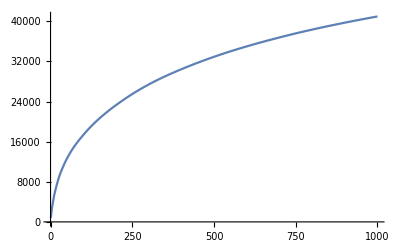

```mathematica
ListPlot[data⟦1,4;;-1,5⟧,Joined->True]
```

```mathematica
data⟦1,203,5⟧
```

23275.8

```mathematica
data⟦1,1003,5⟧
```

40968.4

```mathematica
Clear[data]
```

We suppress the output here.

```mathematica
allData=Import["http://research.stlouisfed.org/fred2/data/FEDFUNDS.txt","Table"];
```

We discard the first 11 lines of allData on the first line of code below, and then display the first five lines. Note that 12;; indicates the span from item 12 to the end.

```mathematica
data=allData⟦12;;⟧;
Grid[data⟦1;;5⟧]
```

For | additional | historical | federal | funds | rate | data, | please | see | Daily | 
Federal | Funds | Rate | from | 1928-1954 |  |  |  |  |  | 
(https://fred.stlouisfed.org/categories/33951). |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  | 
The | federal | funds | rate | is | the | interest | rate | at | which | depository

Note that Rest[list] simply drops the first item in a list, in this case the header row {"DATE","VALUE"}. Think: “It’s the rest of the list”. DateListPlot can handle this date format with no problem. The plot shows clearly the high interest rates that prevailed in the years near 1980.

```mathematica
DateListPlot[Rest[data],Joined->True]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{Federal,Funds,Rate,from,1928-1954},{(https://fred.stlouisfed.org/categories/33951).},{},«45»,{August,2007.},{                     (2) Board of Governors of the Federal Reserve System. "Monetary,Policy},«809»} is not a valid dataset or list of datasets.

DateListPlot[{{Federal,Funds,Rate,from,1928-1954},{(https://fred.stlouisfed.org/categories/33951).},{},{The,federal,funds,rate,is,the,interest,rate,at,which,depository},{institutions,trade,federal,funds,(balances,held,at,Federal,Reserve},{Banks),with,each,other,overnight.,When,a,depository,institution,has},{surplus,balances,in,its,reserve,account,,it,lends,to,other,banks,in},{need,of,larger,balances.,In,simpler,terms,,a,bank,with,excess,cash,},{which,is,often,referred,to,as,liquidity,,will,lend,to,another,bank},{that,needs,to,quickly,raise,liquidity.,(1),The,rate,that,the,borrowing},{institution,pays,to,the,lending,institution,is,determined,between,the},{two,banks;,the,weighted,average,rate,for,all,of,these,types,of},{negotiations,is,called,the,effective,federal,funds,rate.(2),The},{effective,federal,funds,rate,is,essentially,determined,by,the,market},{but,is,influenced,by,the,Federal,Reserve,through,open,market},{operations,to,reach,the,federal,funds,rate,target.(2)},{The,Federal,Open,Market,Committee,(FOMC),meets,eight,times,a,year,to},{determine,the,federal,funds,target,rate.,As,previously,stated,,this},{rate,influences,the,effective,federal,funds,rate,through,open,market},{operations,or,by,buying,and,selling,of,government,bonds,(government},{debt).(2),More,specifically,,the,Federal,Reserve,decreases,liquidity},{by,selling,government,bonds,,thereby,raising,the,federal,funds,rate},{because,banks,have,less,liquidity,to,trade,with,other,banks.},{Similarly,,the,Federal,Reserve,can,increase,liquidity,by,buying},{government,bonds,,decreasing,the,federal,funds,rate,because,banks,have},{excess,liquidity,for,trade.,Whether,the,Federal,Reserve,wants,to,buy},{or,sell,bonds,depends,on,the,state,of,the,economy.,If,the,FOMC},{believes,the,economy,is,growing,too,fast,and,inflation,pressures,are},{inconsistent,with,the,dual,mandate,of,the,Federal,Reserve,,the},{Committee,may,set,a,higher,federal,funds,rate,target,to,temper},{economic,activity.,In,the,opposing,scenario,,the,FOMC,may,set,a,lower},{federal,funds,rate,target,to,spur,greater,economic,activity.},{Therefore,,the,FOMC,must,observe,the,current,state,of,the,economy,to},{determine,the,best,course,of,monetary,policy,that,will,maximize},{economic,growth,while,adhering,to,the,dual,mandate,set,forth,by},{Congress.,In,making,its,monetary,policy,decisions,,the,FOMC,considers},{a,wealth,of,economic,data,,such,as:,trends,in,prices,and,wages,},{employment,,consumer,spending,and,income,,business,investments,,and},{foreign,exchange,markets.},{The,federal,funds,rate,is,the,central,interest,rate,in,the,U.S.},{financial,market.,It,influences,other,interest,rates,such,as,the,prime},{rate,,which,is,the,rate,banks,charge,their,customers,with,higher},{credit,ratings.,Additionally,,the,federal,funds,rate,indirectly},{influences,longer-,term,interest,rates,such,as,mortgages,,loans,,and},{savings,,all,of,which,are,very,important,to,consumer,wealth,and},{confidence.(2)},{References},{(1),Federal,Reserve,Bank,of,New,York.,Federal funds.,Fedpoints,},{August,2007.},{                     (2) Board of Governors of the Federal Reserve System. "Monetary,Policy},{                     (http://www.federalreserve.gov/monetarypolicy/default.htm)".},{},{DATE,VALUE},{1954-07-01,0.8},{1954-08-01,1.22},{1954-09-01,1.07},{1954-10-01,0.85},{1954-11-01,0.83},{1954-12-01,1.28},{1955-01-01,1.39},{1955-02-01,1.29},{1955-03-01,1.35},{1955-04-01,1.43},{1955-05-01,1.43},{1955-06-01,1.64},{1955-07-01,1.68},{1955-08-01,1.96},{1955-09-01,2.18},{1955-10-01,2.24},{1955-11-01,2.35},{1955-12-01,2.48},{1956-01-01,2.45},{1956-02-01,2.5},{1956-03-01,2.5},{1956-04-01,2.62},{1956-05-01,2.75},{1956-06-01,2.71},{1956-07-01,2.75},{1956-08-01,2.73},{1956-09-01,2.95},{1956-10-01,2.96},{1956-11-01,2.88},{1956-12-01,2.94},{1957-01-01,2.84},{1957-02-01,3.},{1957-03-01,2.96},{1957-04-01,3.},{1957-05-01,3.},{1957-06-01,3.},{1957-07-01,2.99},{1957-08-01,3.24},{1957-09-01,3.47},{1957-10-01,3.5},{1957-11-01,3.28},{1957-12-01,2.98},{1958-01-01,2.72},{1958-02-01,1.67},{1958-03-01,1.2},{1958-04-01,1.26},{1958-05-01,0.63},{1958-06-01,0.93},{1958-07-01,0.68},{1958-08-01,1.53},{1958-09-01,1.76},{1958-10-01,1.8},{1958-11-01,2.27},{1958-12-01,2.42},{1959-01-01,2.48},{1959-02-01,2.43},{1959-03-01,2.8},{1959-04-01,2.96},{1959-05-01,2.9},{1959-06-01,3.39},{1959-07-01,3.47},{1959-08-01,3.5},{1959-09-01,3.76},{1959-10-01,3.98},{1959-11-01,4.},{1959-12-01,3.99},{1960-01-01,3.99},{1960-02-01,3.97},{1960-03-01,3.84},{1960-04-01,3.92},{1960-05-01,3.85},{1960-06-01,3.32},{1960-07-01,3.23},{1960-08-01,2.98},{1960-09-01,2.6},{1960-10-01,2.47},{1960-11-01,2.44},{1960-12-01,1.98},{1961-01-01,1.45},{1961-02-01,2.54},{1961-03-01,2.02},{1961-04-01,1.49},{1961-05-01,1.98},{1961-06-01,1.73},{1961-07-01,1.17},{1961-08-01,2.},{1961-09-01,1.88},{1961-10-01,2.26},{1961-11-01,2.61},{1961-12-01,2.33},{1962-01-01,2.15},{1962-02-01,2.37},{1962-03-01,2.85},{1962-04-01,2.78},{1962-05-01,2.36},{1962-06-01,2.68},{1962-07-01,2.71},{1962-08-01,2.93},{1962-09-01,2.9},{1962-10-01,2.9},{1962-11-01,2.94},{1962-12-01,2.93},{1963-01-01,2.92},{1963-02-01,3.},{1963-03-01,2.98},{1963-04-01,2.9},{1963-05-01,3.},{1963-06-01,2.99},{1963-07-01,3.02},{1963-08-01,3.49},{1963-09-01,3.48},{1963-10-01,3.5},{1963-11-01,3.48},{1963-12-01,3.38},{1964-01-01,3.48},{1964-02-01,3.48},{1964-03-01,3.43},{1964-04-01,3.47},{1964-05-01,3.5},{1964-06-01,3.5},{1964-07-01,3.42},{1964-08-01,3.5},{1964-09-01,3.45},{1964-10-01,3.36},{1964-11-01,3.52},{1964-12-01,3.85},{1965-01-01,3.9},{1965-02-01,3.98},{1965-03-01,4.05},{1965-04-01,4.09},{1965-05-01,4.1},{1965-06-01,4.05},{1965-07-01,4.09},{1965-08-01,4.12},{1965-09-01,4.02},{1965-10-01,4.08},{1965-11-01,4.1},{1965-12-01,4.32},{1966-01-01,4.42},{1966-02-01,4.6},{1966-03-01,4.66},{1966-04-01,4.67},{1966-05-01,4.9},{1966-06-01,5.17},{1966-07-01,5.3},{1966-08-01,5.53},{1966-09-01,5.4},{1966-10-01,5.53},{1966-11-01,5.76},{1966-12-01,5.4},{1967-01-01,4.94},{1967-02-01,5.},{1967-03-01,4.53},{1967-04-01,4.05},{1967-05-01,3.94},{1967-06-01,3.98},{1967-07-01,3.79},{1967-08-01,3.9},{1967-09-01,3.99},{1967-10-01,3.88},{1967-11-01,4.13},{1967-12-01,4.51},{1968-01-01,4.61},{1968-02-01,4.71},{1968-03-01,5.05},{1968-04-01,5.76},{1968-05-01,6.12},{1968-06-01,6.07},{1968-07-01,6.03},{1968-08-01,6.03},{1968-09-01,5.78},{1968-10-01,5.91},{1968-11-01,5.82},{1968-12-01,6.02},{1969-01-01,6.3},{1969-02-01,6.61},{1969-03-01,6.79},{1969-04-01,7.41},{1969-05-01,8.67},{1969-06-01,8.9},{1969-07-01,8.61},{1969-08-01,9.19},{1969-09-01,9.15},{1969-10-01,9.},{1969-11-01,8.85},{1969-12-01,8.97},{1970-01-01,8.98},{1970-02-01,8.98},{1970-03-01,7.76},{1970-04-01,8.1},{1970-05-01,7.95},{1970-06-01,7.61},{1970-07-01,7.21},{1970-08-01,6.62},{1970-09-01,6.29},{1970-10-01,6.2},{1970-11-01,5.6},{1970-12-01,4.9},{1971-01-01,4.14},{1971-02-01,3.72},{1971-03-01,3.71},{1971-04-01,4.16},{1971-05-01,4.63},{1971-06-01,4.91},{1971-07-01,5.31},{1971-08-01,5.57},{1971-09-01,5.55},{1971-10-01,5.2},{1971-11-01,4.91},{1971-12-01,4.14},{1972-01-01,3.51},{1972-02-01,3.3},{1972-03-01,3.83},{1972-04-01,4.17},{1972-05-01,4.27},{1972-06-01,4.46},{1972-07-01,4.55},{1972-08-01,4.81},{1972-09-01,4.87},{1972-10-01,5.05},{1972-11-01,5.06},{1972-12-01,5.33},{1973-01-01,5.94},{1973-02-01,6.58},{1973-03-01,7.09},{1973-04-01,7.12},{1973-05-01,7.84},{1973-06-01,8.49},{1973-07-01,10.4},{1973-08-01,10.5},{1973-09-01,10.78},{1973-10-01,10.01},{1973-11-01,10.03},{1973-12-01,9.95},{1974-01-01,9.65},{1974-02-01,8.97},{1974-03-01,9.35},{1974-04-01,10.51},{1974-05-01,11.31},{1974-06-01,11.93},{1974-07-01,12.92},{1974-08-01,12.01},{1974-09-01,11.34},{1974-10-01,10.06},{1974-11-01,9.45},{1974-12-01,8.53},{1975-01-01,7.13},{1975-02-01,6.24},{1975-03-01,5.54},{1975-04-01,5.49},{1975-05-01,5.22},{1975-06-01,5.55},{1975-07-01,6.1},{1975-08-01,6.14},{1975-09-01,6.24},{1975-10-01,5.82},{1975-11-01,5.22},{1975-12-01,5.2},{1976-01-01,4.87},{1976-02-01,4.77},{1976-03-01,4.84},{1976-04-01,4.82},{1976-05-01,5.29},{1976-06-01,5.48},{1976-07-01,5.31},{1976-08-01,5.29},{1976-09-01,5.25},{1976-10-01,5.02},{1976-11-01,4.95},{1976-12-01,4.65},{1977-01-01,4.61},{1977-02-01,4.68},{1977-03-01,4.69},{1977-04-01,4.73},{1977-05-01,5.35},{1977-06-01,5.39},{1977-07-01,5.42},{1977-08-01,5.9},{1977-09-01,6.14},{1977-10-01,6.47},{1977-11-01,6.51},{1977-12-01,6.56},{1978-01-01,6.7},{1978-02-01,6.78},{1978-03-01,6.79},{1978-04-01,6.89},{1978-05-01,7.36},{1978-06-01,7.6},{1978-07-01,7.81},{1978-08-01,8.04},{1978-09-01,8.45},{1978-10-01,8.96},{1978-11-01,9.76},{1978-12-01,10.03},{1979-01-01,10.07},{1979-02-01,10.06},{1979-03-01,10.09},{1979-04-01,10.01},{1979-05-01,10.24},{1979-06-01,10.29},{1979-07-01,10.47},{1979-08-01,10.94},{1979-09-01,11.43},{1979-10-01,13.77},{1979-11-01,13.18},{1979-12-01,13.78},{1980-01-01,13.82},{1980-02-01,14.13},{1980-03-01,17.19},{1980-04-01,17.61},{1980-05-01,10.98},{1980-06-01,9.47},{1980-07-01,9.03},{1980-08-01,9.61},{1980-09-01,10.87},{1980-10-01,12.81},{1980-11-01,15.85},{1980-12-01,18.9},{1981-01-01,19.08},{1981-02-01,15.93},{1981-03-01,14.7},{1981-04-01,15.72},{1981-05-01,18.52},{1981-06-01,19.1},{1981-07-01,19.04},{1981-08-01,17.82},{1981-09-01,15.87},{1981-10-01,15.08},{1981-11-01,13.31},{1981-12-01,12.37},{1982-01-01,13.22},{1982-02-01,14.78},{1982-03-01,14.68},{1982-04-01,14.94},{1982-05-01,14.45},{1982-06-01,14.15},{1982-07-01,12.59},{1982-08-01,10.12},{1982-09-01,10.31},{1982-10-01,9.71},{1982-11-01,9.2},{1982-12-01,8.95},{1983-01-01,8.68},{1983-02-01,8.51},{1983-03-01,8.77},{1983-04-01,8.8},{1983-05-01,8.63},{1983-06-01,8.98},{1983-07-01,9.37},{1983-08-01,9.56},{1983-09-01,9.45},{1983-10-01,9.48},{1983-11-01,9.34},{1983-12-01,9.47},{1984-01-01,9.56},{1984-02-01,9.59},{1984-03-01,9.91},{1984-04-01,10.29},{1984-05-01,10.32},{1984-06-01,11.06},{1984-07-01,11.23},{1984-08-01,11.64},{1984-09-01,11.3},{1984-10-01,9.99},{1984-11-01,9.43},{1984-12-01,8.38},{1985-01-01,8.35},{1985-02-01,8.5},{1985-03-01,8.58},{1985-04-01,8.27},{1985-05-01,7.97},{1985-06-01,7.53},{1985-07-01,7.88},{1985-08-01,7.9},{1985-09-01,7.92},{1985-10-01,7.99},{1985-11-01,8.05},{1985-12-01,8.27},{1986-01-01,8.14},{1986-02-01,7.86},{1986-03-01,7.48},{1986-04-01,6.99},{1986-05-01,6.85},{1986-06-01,6.92},{1986-07-01,6.56},{1986-08-01,6.17},{1986-09-01,5.89},{1986-10-01,5.85},{1986-11-01,6.04},{1986-12-01,6.91},{1987-01-01,6.43},{1987-02-01,6.1},{1987-03-01,6.13},{1987-04-01,6.37},{1987-05-01,6.85},{1987-06-01,6.73},{1987-07-01,6.58},{1987-08-01,6.73},{1987-09-01,7.22},{1987-10-01,7.29},{1987-11-01,6.69},{1987-12-01,6.77},{1988-01-01,6.83},{1988-02-01,6.58},{1988-03-01,6.58},{1988-04-01,6.87},{1988-05-01,7.09},{1988-06-01,7.51},{1988-07-01,7.75},{1988-08-01,8.01},{1988-09-01,8.19},{1988-10-01,8.3},{1988-11-01,8.35},{1988-12-01,8.76},{1989-01-01,9.12},{1989-02-01,9.36},{1989-03-01,9.85},{1989-04-01,9.84},{1989-05-01,9.81},{1989-06-01,9.53},{1989-07-01,9.24},{1989-08-01,8.99},{1989-09-01,9.02},{1989-10-01,8.84},{1989-11-01,8.55},{1989-12-01,8.45},{1990-01-01,8.23},{1990-02-01,8.24},{1990-03-01,8.28},{1990-04-01,8.26},{1990-05-01,8.18},{1990-06-01,8.29},{1990-07-01,8.15},{1990-08-01,8.13},{1990-09-01,8.2},{1990-10-01,8.11},{1990-11-01,7.81},{1990-12-01,7.31},{1991-01-01,6.91},{1991-02-01,6.25},{1991-03-01,6.12},{1991-04-01,5.91},{1991-05-01,5.78},{1991-06-01,5.9},{1991-07-01,5.82},{1991-08-01,5.66},{1991-09-01,5.45},{1991-10-01,5.21},{1991-11-01,4.81},{1991-12-01,4.43},{1992-01-01,4.03},{1992-02-01,4.06},{1992-03-01,3.98},{1992-04-01,3.73},{1992-05-01,3.82},{1992-06-01,3.76},{1992-07-01,3.25},{1992-08-01,3.3},{1992-09-01,3.22},{1992-10-01,3.1},{1992-11-01,3.09},{1992-12-01,2.92},{1993-01-01,3.02},{1993-02-01,3.03},{1993-03-01,3.07},{1993-04-01,2.96},{1993-05-01,3.},{1993-06-01,3.04},{1993-07-01,3.06},{1993-08-01,3.03},{1993-09-01,3.09},{1993-10-01,2.99},{1993-11-01,3.02},{1993-12-01,2.96},{1994-01-01,3.05},{1994-02-01,3.25},{1994-03-01,3.34},{1994-04-01,3.56},{1994-05-01,4.01},{1994-06-01,4.25},{1994-07-01,4.26},{1994-08-01,4.47},{1994-09-01,4.73},{1994-10-01,4.76},{1994-11-01,5.29},{1994-12-01,5.45},{1995-01-01,5.53},{1995-02-01,5.92},{1995-03-01,5.98},{1995-04-01,6.05},{1995-05-01,6.01},{1995-06-01,6.},{1995-07-01,5.85},{1995-08-01,5.74},{1995-09-01,5.8},{1995-10-01,5.76},{1995-11-01,5.8},{1995-12-01,5.6},{1996-01-01,5.56},{1996-02-01,5.22},{1996-03-01,5.31},{1996-04-01,5.22},{1996-05-01,5.24},{1996-06-01,5.27},{1996-07-01,5.4},{1996-08-01,5.22},{1996-09-01,5.3},{1996-10-01,5.24},{1996-11-01,5.31},{1996-12-01,5.29},{1997-01-01,5.25},{1997-02-01,5.19},{1997-03-01,5.39},{1997-04-01,5.51},{1997-05-01,5.5},{1997-06-01,5.56},{1997-07-01,5.52},{1997-08-01,5.54},{1997-09-01,5.54},{1997-10-01,5.5},{1997-11-01,5.52},{1997-12-01,5.5},{1998-01-01,5.56},{1998-02-01,5.51},{1998-03-01,5.49},{1998-04-01,5.45},{1998-05-01,5.49},{1998-06-01,5.56},{1998-07-01,5.54},{1998-08-01,5.55},{1998-09-01,5.51},{1998-10-01,5.07},{1998-11-01,4.83},{1998-12-01,4.68},{1999-01-01,4.63},{1999-02-01,4.76},{1999-03-01,4.81},{1999-04-01,4.74},{1999-05-01,4.74},{1999-06-01,4.76},{1999-07-01,4.99},{1999-08-01,5.07},{1999-09-01,5.22},{1999-10-01,5.2},{1999-11-01,5.42},{1999-12-01,5.3},{2000-01-01,5.45},{2000-02-01,5.73},{2000-03-01,5.85},{2000-04-01,6.02},{2000-05-01,6.27},{2000-06-01,6.53},{2000-07-01,6.54},{2000-08-01,6.5},{2000-09-01,6.52},{2000-10-01,6.51},{2000-11-01,6.51},{2000-12-01,6.4},{2001-01-01,5.98},{2001-02-01,5.49},{2001-03-01,5.31},{2001-04-01,4.8},{2001-05-01,4.21},{2001-06-01,3.97},{2001-07-01,3.77},{2001-08-01,3.65},{2001-09-01,3.07},{2001-10-01,2.49},{2001-11-01,2.09},{2001-12-01,1.82},{2002-01-01,1.73},{2002-02-01,1.74},{2002-03-01,1.73},{2002-04-01,1.75},{2002-05-01,1.75},{2002-06-01,1.75},{2002-07-01,1.73},{2002-08-01,1.74},{2002-09-01,1.75},{2002-10-01,1.75},{2002-11-01,1.34},{2002-12-01,1.24},{2003-01-01,1.24},{2003-02-01,1.26},{2003-03-01,1.25},{2003-04-01,1.26},{2003-05-01,1.26},{2003-06-01,1.22},{2003-07-01,1.01},{2003-08-01,1.03},{2003-09-01,1.01},{2003-10-01,1.01},{2003-11-01,1.},{2003-12-01,0.98},{2004-01-01,1.},{2004-02-01,1.01},{2004-03-01,1.},{2004-04-01,1.},{2004-05-01,1.},{2004-06-01,1.03},{2004-07-01,1.26},{2004-08-01,1.43},{2004-09-01,1.61},{2004-10-01,1.76},{2004-11-01,1.93},{2004-12-01,2.16},{2005-01-01,2.28},{2005-02-01,2.5},{2005-03-01,2.63},{2005-04-01,2.79},{2005-05-01,3.},{2005-06-01,3.04},{2005-07-01,3.26},{2005-08-01,3.5},{2005-09-01,3.62},{2005-10-01,3.78},{2005-11-01,4.},{2005-12-01,4.16},{2006-01-01,4.29},{2006-02-01,4.49},{2006-03-01,4.59},{2006-04-01,4.79},{2006-05-01,4.94},{2006-06-01,4.99},{2006-07-01,5.24},{2006-08-01,5.25},{2006-09-01,5.25},{2006-10-01,5.25},{2006-11-01,5.25},{2006-12-01,5.24},{2007-01-01,5.25},{2007-02-01,5.26},{2007-03-01,5.26},{2007-04-01,5.25},{2007-05-01,5.25},{2007-06-01,5.25},{2007-07-01,5.26},{2007-08-01,5.02},{2007-09-01,4.94},{2007-10-01,4.76},{2007-11-01,4.49},{2007-12-01,4.24},{2008-01-01,3.94},{2008-02-01,2.98},{2008-03-01,2.61},{2008-04-01,2.28},{2008-05-01,1.98},{2008-06-01,2.},{2008-07-01,2.01},{2008-08-01,2.},{2008-09-01,1.81},{2008-10-01,0.97},{2008-11-01,0.39},{2008-12-01,0.16},{2009-01-01,0.15},{2009-02-01,0.22},{2009-03-01,0.18},{2009-04-01,0.15},{2009-05-01,0.18},{2009-06-01,0.21},{2009-07-01,0.16},{2009-08-01,0.16},{2009-09-01,0.15},{2009-10-01,0.12},{2009-11-01,0.12},{2009-12-01,0.12},{2010-01-01,0.11},{2010-02-01,0.13},{2010-03-01,0.16},{2010-04-01,0.2},{2010-05-01,0.2},{2010-06-01,0.18},{2010-07-01,0.18},{2010-08-01,0.19},{2010-09-01,0.19},{2010-10-01,0.19},{2010-11-01,0.19},{2010-12-01,0.18},{2011-01-01,0.17},{2011-02-01,0.16},{2011-03-01,0.14},{2011-04-01,0.1},{2011-05-01,0.09},{2011-06-01,0.09},{2011-07-01,0.07},{2011-08-01,0.1},{2011-09-01,0.08},{2011-10-01,0.07},{2011-11-01,0.08},{2011-12-01,0.07},{2012-01-01,0.08},{2012-02-01,0.1},{2012-03-01,0.13},{2012-04-01,0.14},{2012-05-01,0.16},{2012-06-01,0.16},{2012-07-01,0.16},{2012-08-01,0.13},{2012-09-01,0.14},{2012-10-01,0.16},{2012-11-01,0.16},{2012-12-01,0.16},{2013-01-01,0.14},{2013-02-01,0.15},{2013-03-01,0.14},{2013-04-01,0.15},{2013-05-01,0.11},{2013-06-01,0.09},{2013-07-01,0.09},{2013-08-01,0.08},{2013-09-01,0.08},{2013-10-01,0.09},{2013-11-01,0.08},{2013-12-01,0.09},{2014-01-01,0.07},{2014-02-01,0.07},{2014-03-01,0.08},{2014-04-01,0.09},{2014-05-01,0.09},{2014-06-01,0.1},{2014-07-01,0.09},{2014-08-01,0.09},{2014-09-01,0.09},{2014-10-01,0.09},{2014-11-01,0.09},{2014-12-01,0.12},{2015-01-01,0.11},{2015-02-01,0.11},{2015-03-01,0.11},{2015-04-01,0.12},{2015-05-01,0.12},{2015-06-01,0.13},{2015-07-01,0.13},{2015-08-01,0.14},{2015-09-01,0.14},{2015-10-01,0.12},{2015-11-01,0.12},{2015-12-01,0.24},{2016-01-01,0.34},{2016-02-01,0.38},{2016-03-01,0.36},{2016-04-01,0.37},{2016-05-01,0.37},{2016-06-01,0.38},{2016-07-01,0.39},{2016-08-01,0.4},{2016-09-01,0.4},{2016-10-01,0.4},{2016-11-01,0.41},{2016-12-01,0.54},{2017-01-01,0.65},{2017-02-01,0.66},{2017-03-01,0.79},{2017-04-01,0.9},{2017-05-01,0.91},{2017-06-01,1.04},{2017-07-01,1.15},{2017-08-01,1.16},{2017-09-01,1.15},{2017-10-01,1.15},{2017-11-01,1.16},{2017-12-01,1.3},{2018-01-01,1.41},{2018-02-01,1.42},{2018-03-01,1.51},{2018-04-01,1.69},{2018-05-01,1.7},{2018-06-01,1.82},{2018-07-01,1.91},{2018-08-01,1.91},{2018-09-01,1.95},{2018-10-01,2.19},{2018-11-01,2.2},{2018-12-01,2.27},{2019-01-01,2.4},{2019-02-01,2.4},{2019-03-01,2.41},{2019-04-01,2.42},{2019-05-01,2.39},{2019-06-01,2.38},{2019-07-01,2.4},{2019-08-01,2.13},{2019-09-01,2.04},{2019-10-01,1.83},{2019-11-01,1.55},{2019-12-01,1.55},{2020-01-01,1.55},{2020-02-01,1.58},{2020-03-01,0.65},{2020-04-01,0.05},{2020-05-01,0.05},{2020-06-01,0.08},{2020-07-01,0.09},{2020-08-01,0.1},{2020-09-01,0.09},{2020-10-01,0.09},{2020-11-01,0.09},{2020-12-01,0.09},{2021-01-01,0.09},{2021-02-01,0.08},{2021-03-01,0.07},{2021-04-01,0.07},{2021-05-01,0.06},{2021-06-01,0.08},{2021-07-01,0.1},{2021-08-01,0.09}},Joined→True]

```mathematica
Clear[data,allData]
```

Look in the Documentation Center for more information on the StringMatchQ and BlankNullSequence (___) commands. See also Section 8.8 on page 446.

```mathematica
Select[CountryData["Properties"],StringMatchQ[#,___~~"Product"~~___]&]
```

{AgriculturalProducts,ElectricityProduction,IndustrialProductionGrowth,NaturalGasProduction,OilProduction}

We proceed as in the previous exercise. This example brings up a subtle but important point: some strings in some data sets have commas in them (note the last entry below). Hence making a Grid or Column is a sensible way to display the output. A simple list (where double quotes are not displayed in StandardForm output) will make it impossible to distinguish between a comma that appears within an item, and one that appears between items!

```mathematica
Select[ChemicalData[],StringMatchQ[#,___~~"ButylEther"~~___]&]//Column
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[liquid hydrogen,___~~ButylEther~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[hydrogen,___~~ButylEther~~___].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[deuterium hydride,___~~ButylEther~~___].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

There are 268 such cities at the time of this writing:

```mathematica
Length[Select[CityData[{All,"UnitedStates"}],CityData[#,"Population"]>100000&]]
```

Greater::nord2: Comparison of 8550405 and 100000 is invalid.

Greater::nord2: Comparison of 3971883 and 100000 is invalid.

Greater::nord2: Comparison of 2720546 and 100000 is invalid.

General::stop: Further output of Greater::nord2 will be suppressed during this calculation.

0

The two inputs below accomplish the same thing, removing the Missing data value from the list.

```mathematica
Select[{1,2,Missing["NotAvailable"],4},NumberQ[#]&]
```

{1,2,4}

```mathematica
Cases[{1,2,Missing["NotAvailable"],4},Except[Missing[_]]]
```

{1,2,4}

The input is given below. To save space, the output is not shown.

```mathematica
Select[CountryData[],NumberQ[CountryData[#,"OilConsumption"]]&]
```

The input is given below. To save space, the output is not shown. Here we use the And command via the && symbol, which returns True only if both of the individual statements are true.

```mathematica
Select[CountryData[],NumberQ[CountryData[#,"OilConsumption"]]&&NumberQ[CountryData[#,"Population"]]&]
```

This sorts the list.

```mathematica
Sort[{10,7,9,8}]
```

{7,8,9,10}

To save space we tweak the final input to display only the first 10 rows.

```mathematica
countryList=Select[CountryData[],NumberQ[CountryData[#,"OilConsumption"]]&&NumberQ[CountryData[#,"Population"]]&];
```

```mathematica
Table[{c,CountryData[c,"Population"],CountryData[c,"OilConsumption"]},{c,countryList}];
```

```mathematica
Sort[%,#1⟦3⟧>#2⟦3⟧&]⟦1;;10⟧//Grid
```

Part::take: Cannot take positions 1 through 10 in {}.

Grid[{}⟦1;;10⟧]

Since "OilConsumption" is given in barrels per day, we multiply by 365 to get barrels per year. This is divided by "Population" to get per capita consumption. To save space we display only the top ten rows.

```mathematica
Table[{c,(365*CountryData[c,"OilConsumption"])/CountryData[c,"Population"]},{c,countryList}];
```

```mathematica
Sort[%,#1⟦2⟧>#2⟦2⟧&]⟦1;;10⟧//Grid
```

Part::take: Cannot take positions 1 through 10 in {}.

Grid[{}⟦1;;10⟧]

One approach is to look at the full table produced above, find the U.S., and count down from the top to find its rank. One could easily add a third column to that table displaying rank. Another approach is through the Position command. The first input below illustrates the basic usage of this command. The next two inputs are used to answer the question. The output shows that the string "UnitedStates" appears in row 22, column 1. Hence the answer is that the U.S. ranks 22nd in per capita oil consumption (at the time of this writing).

```mathematica
Position[{a,b,c,d},c]
```

{{3}}

```mathematica
Sort[Table[{c,(365*CountryData[c,"OilConsumption"])/CountryData[c,"Population"]},{c,countryList}],#1⟦2⟧>#2⟦2⟧&];
```

```mathematica
Position[%,"UnitedStates"]
```

{}

```mathematica
Clear[countryList,data,allData,newData]
```

### Section 3.13

Consider the sequence s[n] with s[1]=100, and with the remaining terms defined by the difference equation s[n]=1.05s[n-1].

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[1]=100, n==1}, {s[n]=1.05s[n-1], n>1}}]
```

```mathematica
s[20]
```

252.695

The AxesOrigin setting pulls the axes off the lower-left data point.

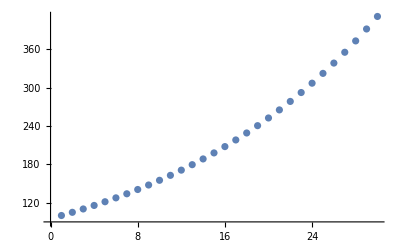

```mathematica
ListPlot[data=Table[{n,s[n]},{n,30}],AxesOrigin->{0,90}]
```

We obtain the formula s[n]=95.2381(1.05)^n. A Plot of this function against the data suggests an excellent fit. Note that in Chapter 4 the task of solving difference equations is handled in a more comprehensive way.

```mathematica
Clear[p,b,n];
FindFit[data,p*b^n,{p,b},n]
```

{p→95.2381,b→1.05}

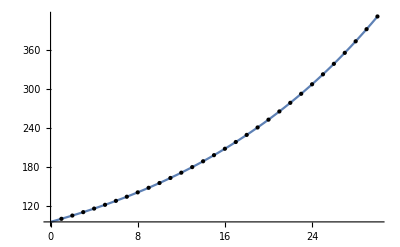

```mathematica
Plot[95.2381(1.05)^n,{n,0,30},Epilog->Point[data]]
```

```mathematica
Clear[data]
```

Letting n denote years and s[n] denote the value of the car after n years, we have s[0]=30000 and s[n]=.90s[n-1] when n>0.

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[0]=30000, n==0}, {s[n]=.90s[n-1], n>0}}]
```

A quick calculation shows that the car is worth $10,460 after 10 years.

```mathematica
s[10]
```

10460.4

Evidently it will take longer than ten years (see part a), but probably not too much longer. A Table of values shows that during the 12th year the value dips below $8,000.

```mathematica
Table[s[n],{n,10,15}];Clear[s]
```